```mathematica
(*Import APC table*)
apcs=Import["Inflation_Inequality/apcs.xlsx"][[1]];
(*Define function for APCs for given country and quintile*)
selectapc[o_,q_]:=Select[apcs,#[[1]]==o&][[1]][[q+2]]/100
(*Load demand shares according to quintile*)
quantiledemand[q_]:=quantiledemand[q]=Import["Inflation_Inequality/Q"<>ToString[q]<>" demand neuer Ansatz final.xlsx"][[1]]

countrypos[o_]:=Position[quantiledemand[1][[2]],o][[1,1]]
(*Define demand for each quintile as a share of income, i.e., by multiplying with the APC*)
quantiledemandcountry[q_,o_]:=Flatten[Append[Drop[Transpose[quantiledemand[q]][[countrypos[o]]],2],ConstantArray[0,56]]]*selectapc[o,q]
(*Import list of Gross Outputs for all Sectors*)
go2014=Import["Inflation/GO_2014.xlsx"][[1,1]];
(*Import WIOD IO table for 2014 w/o labels. Transpose to enable easier division by columns*)
io2014=Transpose[Import["Inflation/IO_2014.xlsx"][[1]]];
(*Calculate technological coefficients by dividing each row (column of original IO table) by corresponding GO value. Transpose back.*)
techcoeff=Transpose[Quiet[Table[io2014[[k]]/go2014[[k]]/. Indeterminate:>0/. ComplexInfinity:>0,{k,1,Length[io2014]}]]];
(*Calculate A*)
leontiefinverse=Inverse[(IdentityMatrix[Length[techcoeff]]-techcoeff)];
Clear[aee,axe]
(*Define (transposed) A matrix with row and column for exogenous sector dropped*)
aee[k_]:=Transpose[Drop[leontiefinverse,{k},{k}]]
(*Take row of exogenous sector, drop own entry and transpose*)
axe[k_]:=Drop[techcoeff[[k]],{k}]
(*Import price time series (intermediate goods price levels, II_PI in WIOD SEA)*)
prices=Import["Inflation/iiprices_full.xlsx"][[1]];
(*Define price shocks as Mean of log differences over all years*)
priceshocks=Table[Mean[Differences[Log[Drop[prices,1][[All,5;;-1]][[k]]]]],{k,1,Length[prices]-1}];
(*Calculate indirect effect as in Weber et al.*)
indirect[k_,q_,c_]:=indirect[k,q,c]=aee[k].axe[k].Drop[quantiledemandcountry[q,c],{k}]*priceshocks[[k]]
(*Calculate direct effect as in Weber et al.*)
direct[k_,q_,c_]:=direct[k,q,c]=quantiledemandcountry[q,c][[k]]*priceshocks[[k]]
(*Load income data*)
incdata=Import["Inflation_Inequality/income_quantiles.csv","CSV"];

(*Define selection function for income wrt country and quantile*)
Clear[selectinc]
countryposinc[c_]:=Flatten[Position[incdata[[All,1]],c]]
countries=DeleteDuplicates[Drop[prices,1][[All,1]]];
selectinc[c_,q_]:=incdata[[countryposinc[c]]][[1]][[q+1]]
(*Define function to find sector position*)
Clear[findsectorpos]
findsectorpos[c_,s_]:=findsectorpos[c,s]=Flatten[Position[Transpose[{Drop[prices,1][[All,1]],Drop[prices,1][[All,4]]}],{c,s}]][[1]]
(*Define function for total effect of a specific sector as a function of demand quantile, demand country, destination country and destination sector*)
Clear[totalpersector]
totalpersector[o_,c_,s_,q_]:=direct[findsectorpos[c,s],q,o]+indirect[findsectorpos[c,s],q,o]
(*Calculate total effect for a specific sector for a given demand country and demand quantile over all destination countries, i.e., L68 in Australia to the USA*)
totalallcountries[o_,s_,q_]:=totalallcountries[o,s,q]=Total[Table[direct[findsectorpos[countries[[i]],s],q,o]+indirect[findsectorpos[countries[[i]],s],q,o],{i,1,Length[countries]}]]

(*Define demand countries as all countries for which we have demand shares in list*)
demandcountries=apcs[[All,1]];
(*Find list of sectors*)
sectors=DeleteDuplicates[Drop[prices[[All,4]],1]];


(*Estimate log-log regression with country FE with income as independent and total effect as dependent variable*)
estimateslog[sector_]:=LinearModelFit[Partition[Flatten[Table[Table[{demandcountries[[i]],Log[selectinc[demandcountries[[i]],q]],Log[totalallcountries[demandcountries[[i]],sector,q]]},{q,1,5}],{i,1,Length[demandcountries]}]],3],{a,b},{a,b},NominalVariables->a]["ParameterTableEntries"][[-1]]
```

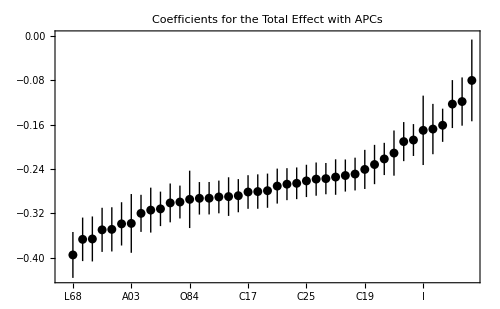

```mathematica
(*Define list of estimates for log-log regressions and order from small to large estimates*)
logestimatelist=SortBy[Quiet[Cases[Table[{estimateslog[sectors[[i]]][[1]],1.96*estimateslog[sectors[[i]]][[2]]},{i,1,Length[sectors]}],{_?NumericQ,_?NumericQ}]],First];
(*Define their labels*)
logestimatelistlabels=SortBy[Quiet[Cases[Table[{sectors[[i]],1.96*estimateslog[sectors[[i]]][[2]],estimateslog[sectors[[i]]][[1]]},{i,1,Length[sectors]}],{_,_?NumericQ,_?NumericQ}]],Last][[All,1]];
(*Define rotation function for ticks in plot*)
tick[s_String]:=Rotate[s,90 Degree];
(*Plot elasticity estimates for total effect*)
ListPlot[Table[Around[logestimatelist[[All,1]][[i]],logestimatelist[[All,2]][[i]]],{i,1,Length[logestimatelist]}],Frame->True,FrameTicks->{{Automatic,None},{Table[{i,tick@logestimatelistlabels[[i]]},{i,1,Length[logestimatelistlabels]}],None}},ImageSize->500,PlotStyle->Black,PlotLabel->"Coefficients for the Total Effect with APCs"]
```

```mathematica
(*Define only direct effect for one sector in all possible destination countries*)
```

```mathematica
totaldirectallcountries[o_,s_,q_]:=Total[Table[direct[findsectorpos[countries[[i]],s],q,o],{i,1,Length[countries]}]]
(*Define only indirect effect for one sector in all possible destination countries*)
totalindirectallcountries[o_,s_,q_]:=Total[Table[indirect[findsectorpos[countries[[i]],s],q,o],{i,1,Length[countries]}]]
```

```mathematica
(*Log-log estimates of elasticity of direct effect with respect to income, including country FE.*)
estimateslogdirect[sector_]:=LinearModelFit[Partition[Flatten[Table[Table[{demandcountries[[i]],Log[selectinc[demandcountries[[i]],q]],Log[totaldirectallcountries[demandcountries[[i]],sector,q]]},{q,1,5}],{i,1,Length[demandcountries]}]],3],{a,b},{a,b},NominalVariables->a]["ParameterTableEntries"][[-1]]
(*Log-log estimates of elasticity of indirect effect with respect to income, including country FE.*)
estimateslogindirect[sector_]:=LinearModelFit[Partition[Flatten[Table[Table[{demandcountries[[i]],Log[selectinc[demandcountries[[i]],q]],Log[totalindirectallcountries[demandcountries[[i]],sector,q]]},{q,1,5}],{i,1,Length[demandcountries]}]],3],{a,b},{a,b},NominalVariables->a]["ParameterTableEntries"][[-1]]
```

```mathematica
(*List of elasticity estimates for direct effect and labels*)
logestimatelistdirect=SortBy[Quiet[Cases[Table[{estimateslogdirect[sectors[[i]]][[1]],1.96*estimateslogdirect[sectors[[i]]][[2]]},{i,1,Length[sectors]}],{_?NumericQ,_?NumericQ}]],First];
logestimatelistlabelsdirect=SortBy[Quiet[Cases[Table[{sectors[[i]],1.96*estimateslogdirect[sectors[[i]]][[2]],estimateslogdirect[sectors[[i]]][[1]]},{i,1,Length[sectors]}],{_,_?NumericQ,_?NumericQ}]],Last][[All,1]];
```

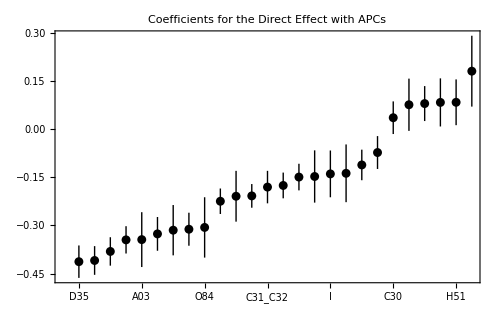

```mathematica
(*Plot of elasticities of direct effect*)
ListPlot[Table[Around[logestimatelistdirect[[All,1]][[i]],logestimatelistdirect[[All,2]][[i]]],{i,1,Length[logestimatelistdirect]}],Frame->True,FrameTicks->{{Automatic,None},{Table[{i,tick@logestimatelistlabelsdirect[[i]]},{i,1,Length[logestimatelistlabelsdirect]}],None}},ImageSize->500,PlotStyle->Black, PlotLabel->"Coefficients for the Direct Effect with APCs"]
```

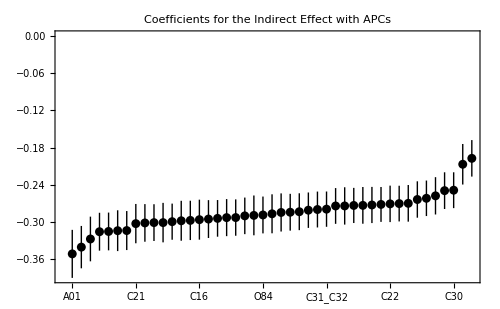

```mathematica
(*List of elasticity estimates for indirect effect*)
logestimatelistindirect=SortBy[Quiet[Cases[Table[{estimateslogindirect[sectors[[i]]][[1]],1.96*estimateslogindirect[sectors[[i]]][[2]]},{i,1,Length[sectors]}],{_?NumericQ,_?NumericQ}]],First];
(*Labels for elasticity estimates for indirect effect*)
logestimatelistlabelsindirect=SortBy[Quiet[Cases[Table[{sectors[[i]],1.96*estimateslogindirect[sectors[[i]]][[2]],estimateslogindirect[sectors[[i]]][[1]]},{i,1,Length[sectors]}],{_,_?NumericQ,_?NumericQ}]],Last][[All,1]];(*Plot of elasticity estimates for the indirect effect*)
ListPlot[Table[Around[logestimatelistindirect[[All,1]][[i]],logestimatelistindirect[[All,2]][[i]]],{i,1,Length[logestimatelistindirect]}],Frame->True,FrameTicks->{{Automatic,None},{Table[{i,tick@logestimatelistlabelsindirect[[i]]},{i,1,Length[logestimatelistlabelsindirect]}],None}},ImageSize->500,PlotStyle->Black,PlotLabel->"Coefficients for the Indirect Effect with APCs",AxesOrigin->{0,0}]
```

```mathematica
(*Export for better plots*)
```

```mathematica
Export["logestimatelisttotalapc.xlsx",Partition[Flatten[Transpose[{logestimatelistlabels,logestimatelist}]],3]]
```

logestimatelisttotalapc.xlsx

```mathematica
Export["logestimatelistdirectapc.xlsx",Partition[Flatten[Transpose[{logestimatelistlabelsdirect,logestimatelistdirect}]],3]]
```

logestimatelistdirectapc.xlsx

```mathematica
Export["logestimatelistindirectapc.xlsx",Partition[Flatten[Transpose[{logestimatelistlabelsindirect,logestimatelistindirect}]],3]]
```

logestimatelistindirectapc.xlsx